## Мухамадиев Владимир

# Задание 3

## Загрузка и предварительная обработка

```mathematica
data1=Import[NotebookDirectory[]<>"\\assoc.txt","Data"];
```

```mathematica
el1=Table[data1⟦i,1⟧<->data1⟦i,2⟧,{i,1,Length[data1]}];
```

```mathematica
g1=Graph[el1];
```

```mathematica
data2=Import[NotebookDirectory[]<>"\\bio-celegans.txt","Data"];
```

```mathematica
el2=Table[data2⟦i,1⟧<->data2⟦i,2⟧,{i,1,Length[data2]}];
```

```mathematica
g2=Graph[el2];
```

```mathematica
data3=Import[NotebookDirectory[]<>"\\bio-diseasome.txt","Data"];
```

```mathematica
el3=Table[data3⟦i,1⟧<->data3⟦i,2⟧,{i,1,Length[data3]}];
```

```mathematica
g3=Graph[el3];
```

```mathematica
data4=Import[NotebookDirectory[]<>"\\ca-AstroPh.txt","Data"];
```

```mathematica
el4=Table[data4⟦i,1⟧<->data4⟦i,2⟧,{i,1,Length[data4]}];
```

```mathematica
g4=Graph[el4];
```

```mathematica
data5=Import[NotebookDirectory[]<>"\\facebook.txt","Data"];
```

```mathematica
el5=Table[data5⟦i,1⟧<->data5⟦i,2⟧,{i,1,Length[data5]}];
```

```mathematica
g5=Graph[el5];
```

```mathematica
data6=Import[NotebookDirectory[]<>"\\proteins.txt","Data"];
```

```mathematica
el6=Table[data6⟦i,1⟧<->data6⟦i,2⟧,{i,1,Length[data6]}];
```

```mathematica
g6=Graph[el6];
```

## 1. Эволюция графа Эрдеша-Реньи и фазовый переход

### Генерация случайного графа Эрдеша-Реньи заданного размера за заданное время

```mathematica
ErdősRenyiGraph[n_,t_]:=Module[{maxe=(n(n-1))/2,am=Table[0,{i,1,n},{j,1,n}],ne=Sort[RandomSample[Range[n],2]]},If[t>maxe,Print["Error: t>n(n-1)/2"],Do[While[am⟦ne⟦1⟧,ne⟦2⟧⟧≠0,ne=Sort[RandomSample[Range[n],2]]];am⟦ne⟦1⟧,ne⟦2⟧⟧=1;am⟦ne⟦2⟧,ne⟦1⟧⟧=1,{k,1,t}];am]]
```

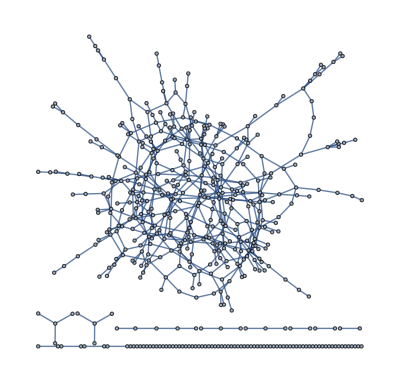

```mathematica
AdjacencyGraph[ErdősRenyiGraph[500,500]]
```

### Генерация эволюции случайного графа Эрдеша-Реньи заданного размера за заданное время

```mathematica
ErdősRenyiGraphList[n_,t_]:=Module[{maxe=(n(n-1))/2,am=Table[0,{i,1,n},{j,1,n}],aml={},ne=Sort[RandomSample[Range[n],2]]},AppendTo[aml,am];If[t>maxe,Print["Error: t>n(n-1)/2"],Do[While[am⟦ne⟦1⟧,ne⟦2⟧⟧≠0,ne=Sort[RandomSample[Range[n],2]]];am⟦ne⟦1⟧,ne⟦2⟧⟧=1;am⟦ne⟦2⟧,ne⟦1⟧⟧=1;AppendTo[aml,am],{k,1,t}];aml]]
```

```mathematica
ergl=ErdősRenyiGraphList[25,25];
```

```mathematica
Manipulate[AdjacencyGraph[ergl⟦l⟧],{l,1,Length[ergl],1}]
```

### Генерация случайного связного графа Эрдеша-Реньи заданного размера

```mathematica
ErdősRenyiConnectedGraph[n_]:=Module[{am=Table[0,{i,1,n},{j,1,n}],ne=Sort[RandomSample[Range[n],2]]},While[ConnectedGraphQ[AdjacencyGraph[am]]≠True,While[am⟦ne⟦1⟧,ne⟦2⟧⟧≠0,ne=Sort[RandomSample[Range[n],2]]];am⟦ne⟦1⟧,ne⟦2⟧⟧=1;am⟦ne⟦2⟧,ne⟦1⟧⟧=1];am]
```

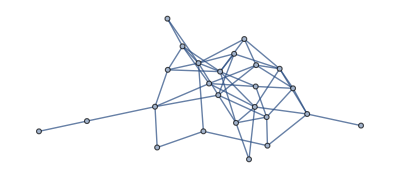

```mathematica
AdjacencyGraph[ErdősRenyiConnectedGraph[25]]
```

### Генерация эволюции случайного графа Эрдеша-Реньи заданного размера до связного состояния

```mathematica
ErdősRenyiConnectedGraphList[n_]:=Module[{am=Table[0,{i,1,n},{j,1,n}],aml={},ne=Sort[RandomSample[Range[n],2]]},AppendTo[aml,am];While[ConnectedGraphQ[AdjacencyGraph[am]]≠True,While[am⟦ne⟦1⟧,ne⟦2⟧⟧≠0,ne=Sort[RandomSample[Range[n],2]]];am⟦ne⟦1⟧,ne⟦2⟧⟧=1;am⟦ne⟦2⟧,ne⟦1⟧⟧=1;AppendTo[aml,am]];aml]
```

```mathematica
ercgl=ErdősRenyiConnectedGraphList[25];
```

```mathematica
Manipulate[AdjacencyGraph[ercgl⟦l⟧],{l,1,Length[ercgl],1}]
```

### Генерация эволюции размеров связных компонент случайного графа Эрдеша-Реньи заданного размера за заданное время

```mathematica
ConnectedComponentsErdősRenyiGaph[n_,t_]:=Module[{am=Table[0,{i,1,n},{j,1,n}],gc=Table[1,{i,1,n}],gcl={},ne=Sort[RandomSample[Range[n],2]]},AppendTo[gcl,gc];Do[While[am⟦ne⟦1⟧,ne⟦2⟧⟧≠0,ne=Sort[RandomSample[Range[n],2]]];am⟦ne⟦1⟧,ne⟦2⟧⟧=1;am⟦ne⟦2⟧,ne⟦1⟧⟧=1;gc=Map[Length,ConnectedComponents[AdjacencyGraph[am]],{1}];AppendTo[gcl,gc],{k,1,t}];gcl]
```

### График эволюции размеров связных компонент случайного графа Эрдеша-Реньи

```mathematica
ConnectedComponentsErdősRenyiGaphPlot[sim_]:=Module[{p0={Length[sim]/2,sim⟦1,Length[sim]/2+1⟧},p1={ReverseSortBy[{Range[Length[sim⟦2⟧]],sim⟦2⟧}ᵀ,Last]⟦1,1⟧,sim⟦1,ReverseSortBy[{Range[Length[sim⟦2⟧]],sim⟦2⟧}ᵀ,Last]⟦1,1⟧+1⟧},p2={Length[sim],sim⟦1,Length[sim]+1⟧}},Show[ListLinePlot[Table[{Range[0,Length[sim⟦1⟧]-1,1],sim⟦i⟧}ᵀ,{i,1,5}],PlotRange->{{0,Length[sim⟦1⟧]},{0,Length[sim]}},AspectRatio->Length[sim]/Length[sim⟦1⟧],GridLines->{p0,p1,p2,{Length[sim⟦1⟧]-1,Length[sim]}}ᵀ,Ticks->{p0,p1,p2,{Length[sim⟦1⟧]-1,Length[sim]},{0,0}}ᵀ,PlotLabel->"График изменения размера пяти самых больших связных компонент в графе",AxesLabel->{"Время","Размер компоненты\n(Число вершин)"},PlotLegends->PointLegend[{Red,Green,Blue},{"Теоретическое время появления гигантской компоненты","Время начала убывания второй по размеру компоненты","Время равно общему числу вершин в графе"},Joined->False]],Graphics[{PointSize[Medium],Red,Point[p0],Green,Point[p1],Blue,Point[p2]}],ImageSize->Full]]
```

#### Однократная генерация

```mathematica
sim1=Import[NotebookDirectory[]<>"\\sim1.m"];(*sim1=N[PadRight[ConnectedComponentsErdősRenyiGaph[500,1500]]]ᵀ;*)
```

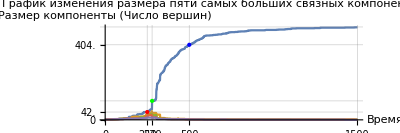

```mathematica
ConnectedComponentsErdősRenyiGaphPlot[sim1]
```

#### Среднее по 10 генерациям

```mathematica
sim10=Import[NotebookDirectory[]<>"\\sim10.m"];(*sim10=Map[Mean,Table[N[PadRight[ConnectedComponentsErdősRenyiGaph[500,1500]]],{l,1,10}]ᵀ,{1}]ᵀ;*)
```

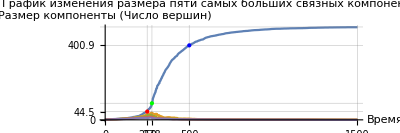

```mathematica
ConnectedComponentsErdősRenyiGaphPlot[sim10]
```

#### Среднее по 100 генерациям

```mathematica
sim100=Import[NotebookDirectory[]<>"\\sim100.m"];(*sim100=Map[Mean,Table[N[PadRight[ConnectedComponentsErdősRenyiGaph[500,1500]]],{l,1,100}]ᵀ,{1}]ᵀ;*)
```

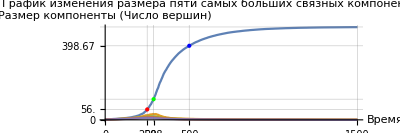

```mathematica
ConnectedComponentsErdősRenyiGaphPlot[sim100]
```

#### Среднее по 1000 генерациям

```mathematica
sim1000=Import[NotebookDirectory[]<>"\\sim1000.m"];(*sim1000=Map[Mean,Table[N[PadRight[ConnectedComponentsErdősRenyiGaph[500,1500]]],{l,1,1000}]ᵀ,{1}]ᵀ;*)
```

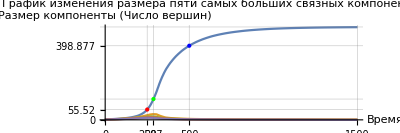

```mathematica
ConnectedComponentsErdősRenyiGaphPlot[sim1000]
```

## 2. Малый мир сложных сетей

### Средний кратчайший путь в графе

```mathematica
MeanShortestPath[graph_]:=Module[{out={},cgc={},cgcd={},cgcdt={}},If[ConnectedGraphQ[graph]==True,out=N[Total[Flatten[GraphDistanceMatrix[graph]]]/(VertexCount[graph]^2-VertexCount[graph])],cgc=ConnectedGraphComponents[graph];cgcd=Table[GraphDistanceMatrix[cgc⟦i⟧],{i,1,Length[cgc]}];cgcdt=Table[If[cgcd⟦i⟧=={{0}},{0,0},{N[Total[Flatten[cgcd⟦i⟧]]/(VertexCount[cgc⟦i⟧]^2-VertexCount[cgc⟦i⟧])],(Length[cgcd⟦i⟧](Length[cgcd⟦i⟧]-1))/2}],{i,1,Length[cgcd]}];out=Total[Table[cgcdt⟦i,1⟧cgcdt⟦i,2⟧,{i,1,Length[cgcdt]}]]/Total[cgcdt⟦All,2⟧]];out]
```

### Оценка среднего кратчайшего пути в графе

```mathematica
EstimatedAveragePath[graph_,numberofvertexpairs_]:=Module[{maxnvp=(VertexCount[graph](VertexCount[graph]-1))/2,gvl=VertexList[graph],eal=Table[0,{i,1,numberofvertexpairs}],rvp={},rvpl={}},If[numberofvertexpairs>maxnvp,Print["Error: number of vertex pairs > n(n-1)/2"],rvp=Sort[RandomSample[gvl,2]];Do[While[MemberQ[rvpl,rvp]==True||FindShortestPath[graph,rvp⟦1⟧,rvp⟦2⟧]=={},rvp=Sort[RandomSample[gvl,2]]];AppendTo[rvpl,rvp];eal⟦i⟧=Length[FindShortestPath[graph,rvp⟦1⟧,rvp⟦2⟧]]-1,{i,1,numberofvertexpairs}];N[Mean[eal]]]]
```

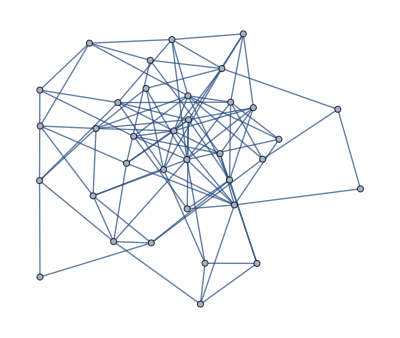

```mathematica
rg=RandomGraph[{35,100}]
```

```mathematica
EstimatedAveragePath[rg,100]
```

2.27

```mathematica
EstimatedAveragePath[rg,595]
```

2.19664

```mathematica
MeanShortestPath[rg]
```

2.19664

### Мера малого мира

```mathematica
Sigma[graph_]:=Module[{c=Mean[LocalClusteringCoefficient[graph]],cr=Mean[VertexDegree[graph]]/VertexCount[graph],l=MeanShortestPath[graph],lr=(Log[VertexCount[graph]]-EulerGamma)/Log[Mean[VertexDegree[graph]]]+1/2},(c lr)/(cr l)]
```

### Параметры графа

```mathematica
GraphParameters[graph_,pairscount_]:={VertexCount[graph],EdgeCount[graph],EstimatedAveragePath[graph,pairscount],MeanShortestPath[graph],N[Log[VertexCount[graph]]],Sigma[graph]}
```

```mathematica
Grid[Prepend[{Prepend[GraphParameters[g1,100],"assoc"],Prepend[GraphParameters[g2,100],"bio-celegans"],Prepend[GraphParameters[g3,100],"bio-diseasome"],Prepend[GraphParameters[g4,100],"ca-AstroPh"],Prepend[GraphParameters[g5,100],"facebook"],Prepend[GraphParameters[g6,100],"proteins"]},{"Name","Vertex count","Edge count","Estimated average path","Mean shortest path","ln(vertex count)","Small-world measure"}],Background->{None,{{{Pink,Lighter[Blue,0.7]}},{1->Gray}}},Dividers->All,Spacings->{1,1}]
```

Name | Vertex count | Edge count | Estimated average path | Mean shortest path | ln(vertex count) | Small-world measure
assoc | 6437 | 36921 | 3.76 | 3.80954 | 8.76982 | 70.2352
bio-celegans | 453 | 2025 | 2.71 | 2.66379 | 6.11589 | 37.2392
bio-diseasome | 516 | 1188 | 6.46 | 6.50899 | 6.24611 | 46.1102
ca-AstroPh | 18771 | 198050 | 4.17 | 4.19399 | 9.84007 | 473.183
facebook | 4039 | 88234 | 3.67 | 3.69251 | 8.30375 | 38.5921
proteins | 335 | 1792 | 4.79 | 4.82131 | 5.81413 | 11.4945

## 3. Устойчивость малого мира сложных сетей

### Удаление заданного процента ребер в графе

```mathematica
DeletePercentEdges[graph_,percent_]:=EdgeDelete[graph,RandomSample[EdgeList[graph],Round[EdgeCount[graph](percent/100)]]]
```

### Сравнение параметров графа и графа с уменьшенным числом ребер

```mathematica
ChangeGraphParameters[graph_,percent_]:=Module[{mg=DeletePercentEdges[graph,percent]},{MeanShortestPath[graph],MeanShortestPath[mg],N[Mean[LocalClusteringCoefficient[graph]]],N[Mean[LocalClusteringCoefficient[mg]]],Sigma[graph],Sigma[mg]}]
```

```mathematica
Grid[Prepend[{Prepend[ChangeGraphParameters[g1,10],"assoc"],Prepend[ChangeGraphParameters[g2,10],"bio-celegans"],Prepend[ChangeGraphParameters[g3,10],"bio-diseasome"],Prepend[ChangeGraphParameters[g4,10],"ca-AstroPh"],Prepend[ChangeGraphParameters[g5,10],"facebook"],Prepend[ChangeGraphParameters[g6,10],"proteins"]},{"Name","Mean shortest path","Mean shortest path (-10%)","Mean Clustering Coefficient","Mean Clustering Coefficient (-10%)","Small-world measure","Small-world measure (-10%)"}],Background->{None,{{{Pink,Lighter[Blue,0.7]}},{1->Gray}}},Dividers->All,Spacings->{1,1}]
```

Name | Mean shortest path | Mean shortest path (-10%) | Mean Clustering Coefficient | Mean Clustering Coefficient (-10%) | Small-world measure | Small-world measure (-10%)
assoc | 3.80954 | 3.884 | 0.123601 | 0.107829 | 70.2352 | 69.3985
bio-celegans | 2.66379 | 2.73836 | 0.646463 | 0.56985 | 37.2392 | 36.9625
bio-diseasome | 6.50899 | 6.79761 | 0.63583 | 0.530088 | 46.1102 | 43.584
ca-AstroPh | 4.19399 | 4.29093 | 0.630627 | 0.553445 | 473.183 | 464.847
facebook | 3.69251 | 3.88242 | 0.605547 | 0.538331 | 38.5921 | 37.0915
proteins | 4.82131 | 5.00884 | 0.653178 | 0.580317 | 11.4945 | 11.3346